```mathematica
dof[m_,n_]:=Simplify[(n(n-1)/2)-((n-m)(n-m-1)/2)]
```

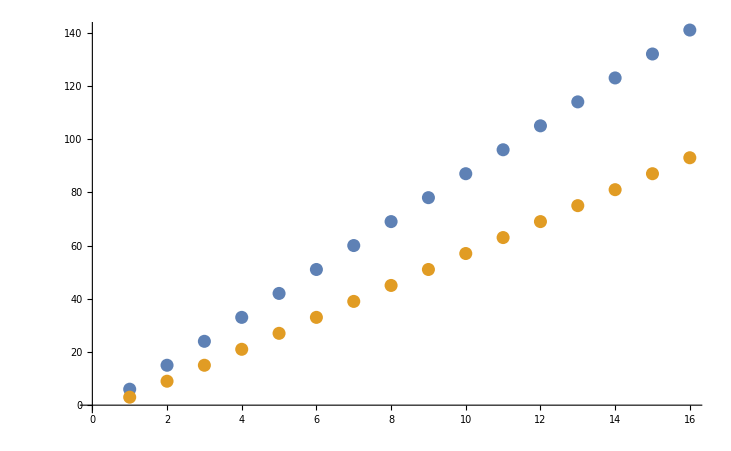

```mathematica
ListPlot[{Table[dof[3,n],{n,4,50,3}],Table[dof[3,n]-(n-1),{n,4,50,3}]}]
```

```mathematica
Collect[dof[m,n],n]
```

-1/2 m (1+m)+m n

```mathematica
Collect[Simplify[dof[m,n]-(n-1)],n]
```

-1/2 (-1+m) (2+m)+(-1+m) n

```mathematica
Collect[Simplify[dof[3,n]],n]
```

-6+3 n

```mathematica
Collect[Simplify[dof[3,n]-(n-1)],n]
```

-5+2 n

```mathematica
Table[{n,dof[3,n],dof[3,n]-(n-1)},{n,4,50,3}]//MatrixForm
```

(4 | 6 | 3
7 | 15 | 9
10 | 24 | 15
13 | 33 | 21
16 | 42 | 27
19 | 51 | 33
22 | 60 | 39
25 | 69 | 45
28 | 78 | 51
31 | 87 | 57
34 | 96 | 63
37 | 105 | 69
40 | 114 | 75
43 | 123 | 81
46 | 132 | 87
49 | 141 | 93)

```mathematica
rot[t_,i_,j_,n_]:=Module[{mm,tt},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[tt],"=",ToString[t],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Cos[tt];mm[[i,j]]=-Sin[tt];mm[[j,i]]=Sin[tt];mm[[j,j]]=Cos[tt];mm)]
```

```mathematica
rot[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[x[2,3]] | -Sin[x[2,3]] | 0
0 | Sin[x[2,3]] | Cos[x[2,3]] | 0
0 | 0 | 0 | 1)

```mathematica
rot2[x_,i_,j_,n_]:=Module[{mm,xx},(mm=IdentityMatrix[n];
ToExpression[StringJoin[ToString[xx],"=",ToString[x],"[",ToString[i],",",ToString[j],"]"]];
mm[[i,i]]=Sqrt[1-xx];mm[[i,j]]=-Sqrt[xx];mm[[j,i]]=Sqrt[xx];mm[[j,j]]=Sqrt[1-xx];mm)]
```

```mathematica
rot2[x,2,3,4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | √(1-x[2,3]) | -√x[2,3] | 0
0 | √x[2,3] | √(1-x[2,3]) | 0
0 | 0 | 0 | 1)

```mathematica
fullRotMat[t_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot[t,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat[t,1,3]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Sin[t[1,2]] | -Cos[t[1,2]] Sin[t[1,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] | -Sin[t[1,2]] Sin[t[1,3]]
Sin[t[1,3]] | 0 | Cos[t[1,3]])

```mathematica
fullRotMat2[x_,m_,n_]:=Module[{mm},(mm=IdentityMatrix[n];For[i=1,i<=n,i++,For[j=i+1,j<=n,j++,If[i<=m||j<=m,mm=mm.rot2[x,i,j,n],Nothing]]];mm)]
```

```mathematica
fullRotMat2[t,1,3]//MatrixForm
```

(√(1-t[1,2]) √(1-t[1,3]) | -√t[1,2] | -√(1-t[1,2]) √t[1,3]
√t[1,2] √(1-t[1,3]) | √(1-t[1,2]) | -√t[1,2] √t[1,3]
√t[1,3] | 0 | √(1-t[1,3]))

```mathematica
sumRows[mm_,m_,n_]:=Table[Sum[Map[Abs,mm][[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
makeEqn[ms_,n_]:=Table[o==ms[[i]],{i,1,n}]
```

```mathematica
trySolve[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRows[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
Table[{2,n,dof[2,n],dof[2,n]-(n-1)},{n,3,5,2}]//MatrixForm
```

(2 | 3 | 3 | 1
2 | 5 | 7 | 3)

```mathematica
Table[{3,n,dof[3,n],dof[3,n]-(n-1)},{n,5,5,3}]//MatrixForm
```

(3 | 5 | 9 | 5)

```mathematica
sumRowsNoAbs[mm_,m_,n_]:=Table[Sum[mm[[j,i]],{i,1,m}],{j,1,n}]
```

```mathematica
trySolveNoAbs[mm_,x_,xmin_,xmax_,m_,n_]:=Module[{mmm,mms,mme},(
mmm=mm;
mms=sumRowsNoAbs[mmm,m,n];
mme=makeEqn[mms,n];
Solve[Join[mme,{0<=o<=1},makeCon[x,m,n,xmin,xmax]],Reals]
)]
```

```mathematica
makeSub[t_,x_,m_,n_]:=Flatten[Table[Table[{Sin[t[i,j]]->Sqrt[x[i,j]],Cos[t[i,j]]->Sqrt[1-x[i,j]]},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x_,m_,n_,xmin_,xmax_]:=Flatten[Table[Table[{xmin<=x[i,j]<=xmax},{j,i+1,n}],{i,1,m}]]
```

```mathematica
makeCon[x,2,3,0,1]
```

{0≤x[1,2]≤1,0≤x[1,3]≤1,0≤x[2,3]≤1}

```mathematica
makeCon[t,2,3,0,2Pi]
```

{0≤t[1,2]≤2 π,0≤t[1,3]≤2 π,0≤t[2,3]≤2 π}

```mathematica
mm=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mmzero=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm2=Table[Table[0,{i,1,20}],{j,1,20}];
```

```mathematica
mm[[2,3]]=fullRotMat[t,2,3];mm2[[2,3]]=fullRotMat2[x,2,3];mm[[2,3]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] | -Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]]
Cos[t[1,3]] Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]] | -Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]]
Sin[t[1,3]] | Cos[t[1,3]] Sin[t[2,3]] | Cos[t[1,3]] Cos[t[2,3]])

```mathematica
mmzero[[2,3]]=mm[[2,3]][[;;,1;;2]]/.{t[1,3]->0};mmzero[[2,3]]//MatrixForm
```

(Cos[t[1,2]] | -Cos[t[2,3]] Sin[t[1,2]]
Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,3]]
0 | Sin[t[2,3]])

```mathematica
FullSimplify[Solve[mmzero[[2,3]][[2,1]]+mmzero[[2,3]][[2,2]]==mmzero[[2,3]][[1,1]]-mmzero[[2,3]][[1,2]],{t[1,2],t[2,3]},Reals]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t[1,2]→ConditionalExpression[1/4 π (1+8 C[1]), C[1]∈ℤ]},{t[1,2]→ConditionalExpression[1/4 π (-3+8 C[1]), C[1]∈ℤ]},{t[2,3]→ConditionalExpression[2 π C[1], C[1]∈ℤ]}}

```mathematica
mmzero00200301=mmzero[[2,3]]/.{t[1,2]->Pi/4};mmzero00200301//MatrixForm
```

(1/(√2) | -Cos[t[2,3]]/(√2)
1/(√2) | Cos[t[2,3]]/(√2)
0 | Sin[t[2,3]])

```mathematica
FullSimplify[Solve[mmzero00200301[[3,1]]+mmzero00200301[[3,2]]==mmzero00200301[[1,1]]-mmzero00200301[[1,2]],{t[2,3]},Reals]]
```

{{t[2,3]→ConditionalExpression[π (-1+4 C[1]), C[1]∈ℤ]},{t[2,3]→ConditionalExpression[π+4 π C[1], C[1]∈ℤ]},{t[2,3]→ConditionalExpression[4 (ArcTan[√(5-2 √6)]+π C[1]), C[1]∈ℤ]},{t[2,3]→ConditionalExpression[-4 ArcTan[√2+√3]+4 π C[1], C[1]∈ℤ]}}

```mathematica
mmzero00200302=FullSimplify[mmzero00200301/.{t[2,3]->4 (ArcTan[√(5-2 √6)])}];mmzero00200302//MatrixForm
```

(1/(√2) | -1/(3 √2)
1/(√2) | 1/(3 √2)
0 | (2 √2)/3)

```mathematica
Solve[o==mmzero00200302[[3,2]],o,Reals]
```

{{o→(2 √2)/3}}

```mathematica
oo=o/.{o->(2 √2)/3};
FullSimplify[(oo)]
N[(oo),50]
FullSimplify[(oo^2)]
N[(oo^2),50]
FullSimplify[(1/oo)]
N[(1/oo),50]
FullSimplify[(1/oo^2)]
N[(1/oo^2),50]
```

(2 √2)/3

0.94280904158206336586779248280646538571311458358463

8/9

0.88888888888888888888888888888888888888888888888889

3/(2 √2)

1.0606601717798212866012665431572735589272539065327

9/8

1.125

```mathematica
mm[[2,5]]=fullRotMat[t,2,5];mm2[[2,5]]=fullRotMat2[x,2,5];mm[[2,5]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] | Cos[t[2,5]] (Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,5]] Sin[t[2,5]] | -Cos[t[1,2]] Cos[t[2,3]] Sin[t[1,3]]+Sin[t[1,2]] Sin[t[2,3]] | -Cos[t[1,2]] Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,4]]-(-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]] | -Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,5]]-(Cos[t[2,4]] (-Cos[t[2,3]] Sin[t[1,2]]-Cos[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,2]] Cos[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]
Cos[t[1,3]] Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,2]] | Cos[t[2,5]] (Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] Sin[t[1,5]] Sin[t[2,5]] | -Cos[t[2,3]] Sin[t[1,2]] Sin[t[1,3]]-Cos[t[1,2]] Sin[t[2,3]] | -Cos[t[1,3]] Cos[t[2,4]] Sin[t[1,2]] Sin[t[1,4]]-(Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]]) Sin[t[2,4]] | -Cos[t[1,3]] Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,2]] Sin[t[1,5]]-(Cos[t[2,4]] (Cos[t[1,2]] Cos[t[2,3]]-Sin[t[1,2]] Sin[t[1,3]] Sin[t[2,3]])-Cos[t[1,3]] Sin[t[1,2]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]
Cos[t[1,4]] Cos[t[1,5]] Sin[t[1,3]] | Cos[t[2,5]] (Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]])-Cos[t[1,4]] Sin[t[1,3]] Sin[t[1,5]] Sin[t[2,5]] | Cos[t[1,3]] Cos[t[2,3]] | -Cos[t[2,4]] Sin[t[1,3]] Sin[t[1,4]]-Cos[t[1,3]] Sin[t[2,3]] Sin[t[2,4]] | -Cos[t[1,4]] Cos[t[2,5]] Sin[t[1,3]] Sin[t[1,5]]-(Cos[t[1,3]] Cos[t[2,4]] Sin[t[2,3]]-Sin[t[1,3]] Sin[t[1,4]] Sin[t[2,4]]) Sin[t[2,5]]
Cos[t[1,5]] Sin[t[1,4]] | Cos[t[1,4]] Cos[t[2,5]] Sin[t[2,4]]-Sin[t[1,4]] Sin[t[1,5]] Sin[t[2,5]] | 0 | Cos[t[1,4]] Cos[t[2,4]] | -Cos[t[2,5]] Sin[t[1,4]] Sin[t[1,5]]-Cos[t[1,4]] Sin[t[2,4]] Sin[t[2,5]]
Sin[t[1,5]] | Cos[t[1,5]] Sin[t[2,5]] | 0 | 0 | Cos[t[1,5]] Cos[t[2,5]])

```mathematica
mmzero[[2,5]]=mm[[2,5]][[;;,1;;2]]/.{t[1,5]->0,t[2,4]->0,t[2,3]->0};mmzero[[2,5]]//MatrixForm
```

(Cos[t[1,2]] Cos[t[1,3]] Cos[t[1,4]] | -Cos[t[2,5]] Sin[t[1,2]]
Cos[t[1,3]] Cos[t[1,4]] Sin[t[1,2]] | Cos[t[1,2]] Cos[t[2,5]]
Cos[t[1,4]] Sin[t[1,3]] | 0
Sin[t[1,4]] | 0
0 | Sin[t[2,5]])

```mathematica
FullSimplify[Solve[mmzero[[2,5]][[2,1]]+mmzero[[2,5]][[2,2]]==mmzero[[2,5]][[1,1]]-mmzero[[2,5]][[1,2]],{t[1,2],t[1,3],t[1,4],t[2,5]},Reals]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t[1,2]→ConditionalExpression[1/4 π (1+8 C[1]), C[1]∈ℤ]},{t[1,2]→ConditionalExpression[1/4 π (-3+8 C[1]), C[1]∈ℤ]},{t[2,5]→ConditionalExpression[-ArcCos[Cos[t[1,3]] Cos[t[1,4]]]+2 π C[1], C[1]∈ℤ]},{t[2,5]→ConditionalExpression[ArcCos[Cos[t[1,3]] Cos[t[1,4]]]+2 π C[1], C[1]∈ℤ]}}

```mathematica
mmzero00200501=mmzero[[2,5]]/.{t[1,2]->Pi/4};mmzero00200501//MatrixForm
```

((Cos[t[1,3]] Cos[t[1,4]])/(√2) | -Cos[t[2,5]]/(√2)
(Cos[t[1,3]] Cos[t[1,4]])/(√2) | Cos[t[2,5]]/(√2)
Cos[t[1,4]] Sin[t[1,3]] | 0
Sin[t[1,4]] | 0
0 | Sin[t[2,5]])

```mathematica
FullSimplify[Solve[mmzero00200501[[4,1]]+mmzero00200501[[4,2]]==mmzero00200501[[5,1]]+mmzero00200501[[5,2]],{t[1,3],t[1,4]},Reals]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{t[1,4]→ConditionalExpression[π-ArcSin[Sin[t[2,5]]]+2 π C[1], C[1]∈ℤ&&-1≤Sin[t[2,5]]≤1]},{t[1,4]→ConditionalExpression[ArcSin[Sin[t[2,5]]]+2 π C[1], C[1]∈ℤ&&-1≤Sin[t[2,5]]≤1]}}

```mathematica
mmzero00200502=mmzero00200501/.{t[1,4]->ArcSin[Sin[t[2,5]]]};mmzero00200502//MatrixForm
```

((Cos[t[1,3]] √(1-Sin[t[2,5]]^2))/(√2) | -Cos[t[2,5]]/(√2)
(Cos[t[1,3]] √(1-Sin[t[2,5]]^2))/(√2) | Cos[t[2,5]]/(√2)
Sin[t[1,3]] √(1-Sin[t[2,5]]^2) | 0
Sin[t[2,5]] | 0
0 | Sin[t[2,5]])

```mathematica
mmzero00200503=FullSimplify[mmzero00200502,Assumptions->Join[{Reals},makeCon[t,2,5,0,Pi/2]]];mmzero00200503//MatrixForm
```

((Cos[t[1,3]] Cos[t[2,5]])/(√2) | -Cos[t[2,5]]/(√2)
(Cos[t[1,3]] Cos[t[2,5]])/(√2) | Cos[t[2,5]]/(√2)
Cos[t[2,5]] Sin[t[1,3]] | 0
Sin[t[2,5]] | 0
0 | Sin[t[2,5]])

```mathematica
FullSimplify[Solve[{mmzero00200503[[4,1]]+mmzero00200503[[4,2]]==mmzero00200503[[3,1]]+mmzero00200503[[3,2]]},{t[1,3]},Reals],Assumptions->Join[{Reals},makeCon[t,2,5,0,Pi/2]]]
```

{{t[1,3]→ConditionalExpression[π-ArcSin[Tan[t[2,5]]]+2 π C[1], C[1]∈ℤ&&Cos[t[2,5]]>0&&Sin[t[2,5]]≤Cos[t[2,5]]]},{t[1,3]→ConditionalExpression[ArcSin[Tan[t[2,5]]]+2 π C[1], C[1]∈ℤ&&Cos[t[2,5]]>0&&Sin[t[2,5]]≤Cos[t[2,5]]]}}

```mathematica
mmzero00200504=FullSimplify[mmzero00200503/.{t[1,3]->ArcSin[Tan[t[2,5]]]},Assumptions->Join[{Reals},makeCon[t,2,5,0,Pi/2]]];mmzero00200504//MatrixForm
```

(Cos[t[2,5]] √(1-1/2 Sec[t[2,5]]^2) | -Cos[t[2,5]]/(√2)
Cos[t[2,5]] √(1-1/2 Sec[t[2,5]]^2) | Cos[t[2,5]]/(√2)
Sin[t[2,5]] | 0
Sin[t[2,5]] | 0
0 | Sin[t[2,5]])

```mathematica
FullSimplify[Solve[mmzero00200504[[4,1]]+mmzero00200504[[4,2]]==mmzero00200504[[2,1]]+mmzero00200504[[2,2]],{t[2,5]},Reals]]
```

{{t[2,5]→ConditionalExpression[2 (ArcTan[(-3+√17)/(2 √2)]+π C[1]), C[1]∈ℤ]},{t[2,5]→ConditionalExpression[-2 ArcTan[(3+√17)/(2 √2)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
mmzero00200505=FullSimplify[mmzero00200504/.{t[2,5]->2 (ArcTan[(-3+√17)/(2 √2)])},Assumptions->Join[{Reals},makeCon[t,2,5,0,Pi/2]]];mmzero00200505//MatrixForm
```

(1/(√34) | -3/(√34)
1/(√34) | 3/(√34)
2 √(2/17) | 0
2 √(2/17) | 0
0 | 2 √(2/17))

```mathematica
Solve[mmzero00200505[[4,1]]-mmzero00200505[[4,2]]==o,o,Reals]
```

{{o→2 √(2/17)}}

```mathematica
oo=o/.{o->2 √(2/17)};
FullSimplify[(oo)]
N[(oo),50]
FullSimplify[(oo^2)]
N[(oo^2),50]
FullSimplify[(1/oo)]
N[(1/oo),50]
FullSimplify[(1/oo^2)]
N[(1/oo^2),50]
```

2 √(2/17)

0.68599434057003534951460622088771565606134098057482

8/17

0.47058823529411764705882352941176470588235294117647

(√(17/2))/2

1.4577379737113251177185382193863957691303495837215

17/8

2.125